```mathematica
sol=DSolve[{y'[x]+y[x]*Tan[x]==Sin[2x] , y[0]==0},y[x], x]
```

{{y[x]→-2 (-Cos[x]+Cos[x]^2)}}

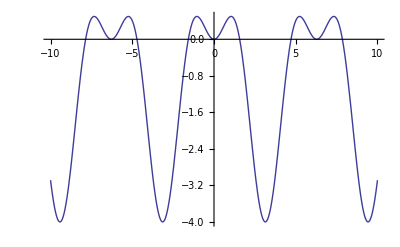

```mathematica
Plot[Evaluate[y[x]/.sol[[1]]], {x, -10, 10}]
```

```mathematica
Manipulate[
Plot[
Evaluate[
у[x]/.First[DSolve[{a*y''[x]+b*y'[x]+c*y[x]== 0 , y[0]==0, y'[0]==1},y, x]]], 
{x, -10, 10}],{a, -20, 20}, {b,-20, 20}, {c, -20, 20}]
```

```mathematica
Plot[Evaluate[y[x]/.sol[[1]]], {x, -10, 10}]
```

-Graphics-